```mathematica
sf=Import["G:\\calc-online\\polarized\\spf\\numcalc\\spfnumre\\spf-rbw-oct-ξ1-L1.wdx"];
ft1=Query[1,1]@sf;
ft2=Query[2,1]@sf;
gt1=Query[1,2]@sf;
gt2=Query[2,2]@sf;
fp1=Interpolation[Flatten[ft1,1]];
fp2=Interpolation[Flatten[ft2,1]];
gp1=Interpolation[Flatten[gt1,1]];
gp2=Interpolation[Flatten[gt2,1]];
```

```mathematica
rfp1[x_,t_]=0.5*0.05888785346404517*x*fp1[x,t];
rfp2[x_,t_]=0.5*0.05888785346404517*x*fp2[x,t];
rgp1[x_,t_]=0.5*0.05888785346404517*x*gp1[x,t];
rgp2[x_,t_]=0.5*0.05888785346404517*x*gp2[x,t];
```

```mathematica
fn=Show[Plot3D[-I*fp1[x,t],{x,0,0.9},{t,-1,-0.037},PlotRange->All],Plot3D[-I*fp2[x,t],{x,0.9,1.1},{t,-1,-0.037},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.55,-.20,0}]]],Graphics3D[Text[Style["t (GeV^2)",Black,30,FontFamily->Times],Scaled[{1.22,0.3,0.2}]]],
Graphics3D[Text[Style["f(y)",Black,30,FontSlant->Italic,FontFamily->Times],Scaled[{-0.1,-.25,0.65}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{2,-2.2,1.4}]
```

-Graphics3D-

```mathematica
Show[Plot3D[-I*x*fp1[x,t],{x,0,0.9},{t,-1,-0.037},PlotRange->All],Plot3D[-I*x*fp2[x,t],{x,0.9,1.1},{t,-1,-0.037},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.55,-.20,0}]]],Graphics3D[Text[Style["t (GeV^2)",Black,30,FontFamily->Times],Scaled[{1.22,0.3,0.2}]]],
Graphics3D[Text[Style["f(y)",Black,30,FontSlant->Italic,FontFamily->Times],Scaled[{-0.1,-.25,0.65}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{2,-2.2,1.4}]
```

-Graphics3D-

```mathematica
gn=Show[Plot3D[Re[-I*gp1[x,t]],{x,0,0.9},{t,-1,-0.037},PlotRange->All],Plot3D[Re[-I*gp2[x,t]],{x,0.9,1.1},{t,-1,-0.037},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.55,-.20,0}]]],Graphics3D[Text[Style["-t (GeV^2)",Black,30,FontFamily->Times],Scaled[{1.22,0.3,0.2}]]],
Graphics3D[Text[Style["g_(π^+ n)(y)",Black,30,FontSlant->Italic,FontFamily->Times],Scaled[{-0.1,-.25,0.65}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{2,-2.2,1.4}]
```

-Graphics3D-

```mathematica
Show[Plot3D[Re[-I*x*gp1[x,t]],{x,0,0.9},{t,-1,-0.037},PlotRange->All],Plot3D[Re[-I*x*gp2[x,t]],{x,0.9,1.1},{t,-1,-0.037},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.55,-.20,0}]]],Graphics3D[Text[Style["-t (GeV^2)",Black,30,FontFamily->Times],Scaled[{1.22,0.3,0.2}]]],
Graphics3D[Text[Style["g_(π^+ n)(y)",Black,30,FontSlant->Italic,FontFamily->Times],Scaled[{-0.1,-.25,0.65}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{2,-2.2,1.4}]
```

-Graphics3D-

```mathematica
pathf=FileNameJoin[{"G:\\calc-online\\polarized\\spf\\pic","rbw-q0-spinsum.pdf"}];
Export[pathf,fn]
```

G:\calc-online\polarized\spf\pic\rbw-q0-spinsum.pdf

```mathematica
pathf=FileNameJoin[{"G:\\calc-online\\polarized\\spf\\pic","rbw-q0.pdf"}];
Export[pathf,fn]
```

G:\calc-online\polarized\spf\pic\rbw-q0.pdf

```mathematica
coe=(0.5+0.76/3)^2/(0.093)^2*1/(2*(2π)^4)
```

0.0210503

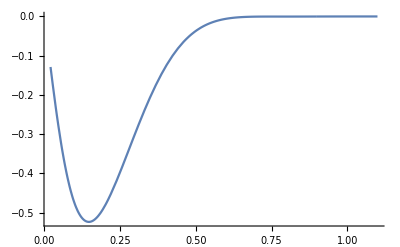

```mathematica
Show[Plot[-I*coe*fp1[x,-1],{x,0,0.9},PlotRange->All],Plot[-I*coe*fp2[x,-1],{x,0.9,1.1},PlotRange->All]]
```

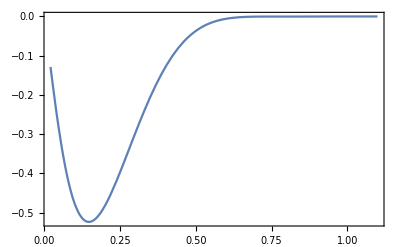
-Graphics-f̃yξ=0.1

```mathematica
picf=Labeled[Show[Plot[-I*coe*fp1[x,-1],{x,0,0.9},PlotRange->All],Plot[-I*coe*fp2[x,-1],{x,0.9,1.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"\!\(\*TagBox[OverscriptBox[\"f\", \"~\"],DisplayForm]\)","y","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

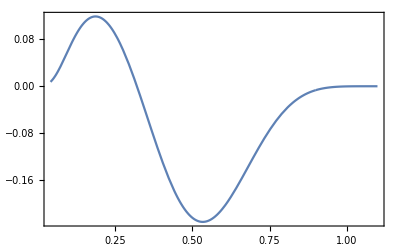
-Graphics-g̃yξ=0.1

```mathematica
picg=Labeled[Show[Plot[-I*coe*gp1[x,-1],{x,0,0.9},PlotRange->All],Plot[-I*coe*gp2[x,-1],{x,0.9,1.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"\!\(\*TagBox[OverscriptBox[\"g\", \"~\"],DisplayForm]\)","y","ξ=0.1"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
pathf2d=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\中期报告\\pic","polar-spf-rainbow-oct-f.pdf"}];
Export[pathf2d,picf]
```

C:\Users\DELL\Desktop\中期报告\pic\polar-spf-rainbow-oct-f.pdf

```mathematica
pathg2d=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\中期报告\\pic","polar-spf-rainbow-oct-g.pdf"}];
Export[pathg2d,picg]
```

C:\Users\DELL\Desktop\中期报告\pic\polar-spf-rainbow-oct-g.pdf

```mathematica
OverscriptBox["f","~"]//DisplayForm
```

f̃

```mathematica
FontSlant->Italic,FontFamily->Times
```

```mathematica
Style["f̃",FontSlant->Italic,FontFamily->Times]
```

f̃

```mathematica
OverscriptBox["g","~"]//DisplayForm
```

g̃

```mathematica
Style["g̃",FontSlant->Italic,FontFamily->Times]
```

g̃